```mathematica
f[x_]:=Sinh[x-1]/(1-Log[(x+3)/5]) (*definice funkce pro generaci bodů k interpolaci*)
```

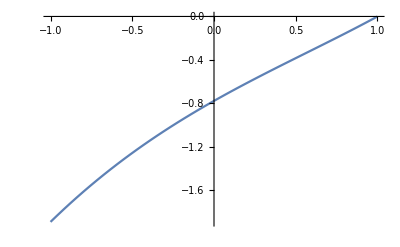

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
Nn=16
```

```mathematica
c=Table[2/Nn*Sum[f[Cos[Pi*(k-0.5)/Nn]]*Cos[Pi*j*(k-0.5)/Nn],{k,1,Nn}],{j,0,Nn-1}]
```

```mathematica
ListLogPlot[Abs[c]] (*koeficienty příspěvků od jednotlivých Čebyševových polynomů*)
```

```mathematica
Plot[{c[[1]]/2+Sum[c[[j+1]]*ChebyshevT[j,x],{j,1,Nn-1}],f[x]},{x,-1,1}]
```

chyba interpolace Čebyševovým polynomem

```mathematica
LogPlot[Abs[c[[1]]/2+Sum[c[[j+1]]*ChebyshevT[j,x],{j,1,Nn-1}]-f[x]],{x,-1,1}](* je vidět, že na krajích intervalu se "zahušťují" interpolační body, tím se předchází Rungeovu jevu*)
```

```mathematica
g[x_]:=(10*x)^4*Log[10+Abs[10*x]]*Cos[10*x] (*úkol: interpolujte funkci g pro N=20 nulových bodů*)
```